```mathematica
APV′general=((gL-gR) gV Q2)/(4 mz^2 π α)+((gLp-gRp) gVp Q2)/(4 π (mzp^2+Q2) α);
quark′proton′rep={gV->2gVu+gVd,gVp->2gVup+gVdp};(*p means prime in Z' *)

quark′C12′rep={gV->6(2gVu+gVd)+6(gVu+2gVd),gVp->6(2gVup+gVdp)+6(gVup+2gVdp)};(*p means prime in Z' *)
quark′Cs133′rep={gV->55(2gVu+gVd)+(133-55)(gVu+2gVd),gVp->55(2gVup+gVdp)+(133-55)(gVup+2gVdp)};(*p means prime in Z' *)

APV=APV′general/.quark′proton′rep;
APV′C12=APV′general/.quark′C12′rep;
APV′Cs133=APV′general/.quark′Cs133′rep;

gzmz={gz->(√(4 π α))/(sw cw),mz->((π α)/(√2 GF sw^2 cw^2) )^(1/2)};
gSM′rep={
(****SM coupling to leptons******)
gLSM->gz(-1/2+sw^2)(*Z coupling to eL*),
gRSM->gz sw^2(*Z coupling to eR*),
gνLSM->gz(1/2)(*Z coupling to νL*),
gνRSM->0(*Z coupling to νR*),

(****SM coupling to quarks******)
gVuSM->gz (1/4-2/3 sw^2),gVdSM->gz (-1/4+1/3 sw^2),
guLSM->gz (1/2-2/3 sw^2),guRSM->gz (-2/3 sw^2),
gdLSM->gz (-1/2+1/3 sw^2),gdRSM->gz (1/3 sw^2)
};

(*Note: {gVuSM-(guLSM+guRSM)/2,gVdSM-(gdLSM+gdRSM)/2}/.gSM′rep//Simplify should be 0*)


APV′SM=APV/.
{gL->gLSM,gR->gRSM,gVu->gVuSM,gVd->gVdSM,gVup->0,gVdp->0}/.gSM′rep//Simplify;
APV′relative=APV/APV′SM//Simplify;
Print["SM contibution to APV= ", APV′SM/.gzmz//Simplify]
Print["New physics (Z') contibution/SM contibution= ", APV′relative]

APV′SM′C12=APV′C12/.
{gL->gLSM,gR->gRSM,gVu->gVuSM,gVd->gVdSM,gVup->0,gVdp->0}/.gSM′rep//Simplify;
APV′relative′C12=APV′C12/APV′SM′C12//Simplify;
Print["SM contibution to APV for^12C= ", APV′SM′C12/.gzmz//Simplify]
Print["New physics (Z') contibution/SM contibution for^12C= ", APV′relative′C12]

APV′SM′Cs133=APV′Cs133/.
{gL->gLSM,gR->gRSM,gVu->gVuSM,gVd->gVdSM,gVup->0,gVdp->0}/.gSM′rep//Simplify;
APV′relative′Cs133=APV′Cs133/APV′SM′Cs133//Simplify;
APV′relative′Cs133=APV′relative′Cs133/.Q2->Q2Cs133
```

SM contibution to APV= (GF Q2 (-1+4 sw^2))/(4 √2 π α)

New physics (Z') contibution/SM contibution= (8 (gLp (gVdp+2 gVup) mz^2-gRp (gVdp+2 gVup) mz^2+(gL-gR) (gVd+2 gVu) (mzp^2+Q2)))/(gz^2 (mzp^2+Q2) (-1+4 sw^2))

SM contibution to APV for^12C= (3 √2 GF Q2 sw^2)/(π α)

New physics (Z') contibution/SM contibution for^12C= (6 (gLp (gVdp+gVup) mz^2-gRp (gVdp+gVup) mz^2+(gL-gR) (gVd+gVu) (mzp^2+Q2)))/(gz^2 (mzp^2+Q2) sw^2)

(8 (gLp (211 gVdp+188 gVup) mz^2-gRp (211 gVdp+188 gVup) mz^2+(gL-gR) (211 gVd+188 gVu) (mzp^2+Q2Cs133)))/(gz^2 (mzp^2+Q2Cs133) (23+220 sw^2))

-Graphics-

-Graphics-

```mathematica
(*√Q2/.parameters*)
```

```mathematica
parameters={
GeV->10^3 MeV,
(***SM paramters*****)
GF->1.166 10^-5  GeV^-2, α->1/137,cw->√(1-sw^2),sw->√0.23,mz->91.19 GeV,
(***P2 experiment parameters *****)
Q2->4. 155 155 Sin[35°/2]^2 MeV^2,
Q2Cs133->(30 MeV)^2,
precision->0.014 ×√2.71,
precision′C12->0.003 ×√2.71,
Print["Cs133 precision",temp=(√(0.26^2+0.23^2)/73.71)];
precision′Cs133->temp×√2.71
(*0.014 comes from our draft;
0.003  comes from Sec.7.1.2 in the P2 paper;
2.71 from Table 39.2 in PDG2018. 
It converts 1σ uncertainty to 90%CL*)};
Print["tree-level SM APV=",APV′SM/.gzmz//.parameters]
Print["tree-level SM APV for C12=",APV′SM′C12/.gzmz//.parameters]
```

Cs133 precision0.00470942

tree-level SM APV=-6.24872×10^-8

tree-level SM APV for C12=4.31162×10^-6

0.00470942

## New physics Models

```mathematica
addV[model_]:=Join[model,<|gVu->(guL+guR)/2,gVd->(gdL+gdR)/2,gVup->(guLp+guRp)/2,gVdp->(gdLp+gdRp)/2|>/.model]//Simplify;

gorder={gLp,gRp,gνLp,gνRp,guLp,gdLp,guRp,gdRp};
Qorder={ QL,  QR,  QνL, QνR,   QuL,   QdL,  QuR,   QdR};

add′gx[model_]:=(model′new=model;
Table[xxx=gorder⟦i⟧;
model′new[xxx]=model[xxx]+gx Qorder⟦i⟧,{i,Length[gorder]}];
model′new
)



θmodel=<|
gLp->-gLSM sθ,gRp->-gRSM sθ,
gνLp->-gνLSM sθ,gνRp->-gνRSM sθ,
guLp->-guLSM sθ,gdLp->-gdLSM sθ,
guRp->-guRSM sθ,gdRp->-gdRSM sθ,

gL->gLSM cθ,gR->gRSM cθ,
gνL->gνLSM cθ,gνR->gνRSM cθ,
guL->guLSM cθ,gdL->gdLSM cθ,
guR->guRSM cθ,gdR->gdRSM cθ|>;

θxmodel=add′gx[θmodel];


ϵmodel=<|
gLp->(Subscript[g, Z] Subscript[s, W] (-2+Subscript[r, m]+2 Subscript[s, W]^2) ϵ)/(2 (-1+Subscript[r, m])),gRp->(Subscript[g, Z] Subscript[s, W] (-1+Subscript[r, m]+Subscript[s, W]^2) ϵ)/(-1+Subscript[r, m]),
gνLp->(Subscript[g, Z] Subscript[r, m] Subscript[s, W] ϵ)/(2 (-1+Subscript[r, m])),gνRp->0,

guLp->-((Subscript[g, Z] Subscript[s, W] (-4+Subscript[r, m]+4 Subscript[s, W]^2)) ϵ)/(6 (-1+Subscript[r, m])),gdLp->(Subscript[g, Z] Subscript[s, W] (-2-Subscript[r, m]+2 Subscript[s, W]^2) ϵ)/(6 (-1+Subscript[r, m])),
guRp->-(2 (Subscript[g, Z] Subscript[s, W] (-1+Subscript[r, m]+Subscript[s, W]^2)) ϵ)/(3 (-1+Subscript[r, m])),gdRp->(Subscript[g, Z] Subscript[s, W] (-1+Subscript[r, m]+Subscript[s, W]^2) ϵ)/(3 (-1+Subscript[r, m])),

gL->gLSM -((Subscript[g, Z] Subscript[s, W]^2 (-3+2 Subscript[r, m]+2 Subscript[s, W]^2)) ϵ^2)/(4 (-1+Subscript[r, m])^2),gR->gRSM -((Subscript[g, Z] Subscript[s, W]^2 (-2+2 Subscript[r, m]+Subscript[s, W]^2)) ϵ^2)/(2 (-1+Subscript[r, m])^2),
gνL->gνLSM +(Subscript[g, Z] (1-2 Subscript[r, m]) Subscript[s, W]^2 ϵ^2)/(4 (-1+Subscript[r, m])^2),gνR->gνRSM +0,
guL->guLSM +(Subscript[g, Z] Subscript[s, W]^2 (-5+2 Subscript[r, m]+4 Subscript[s, W]^2) ϵ^2)/(12 (-1+Subscript[r, m])^2),gdL->gdLSM -((Subscript[g, Z] Subscript[s, W]^2 (-1-2 Subscript[r, m]+2 Subscript[s, W]^2)) ϵ^2)/(12 (-1+Subscript[r, m])^2),
guR->guRSM+(Subscript[g, Z] Subscript[s, W]^2 (-2+2 Subscript[r, m]+Subscript[s, W]^2) ϵ^2)/(3 (-1+Subscript[r, m])^2),gdR->gdRSM -((Subscript[g, Z] Subscript[s, W]^2 (-2+2 Subscript[r, m]+Subscript[s, W]^2)) ϵ^2)/(6 (-1+Subscript[r, m])^2)|>/.{Subscript[r, m]->rm,Subscript[s, W]->sw, Subscript[g, Z]->gz};

(**chiral U(1) ****)
SMpart=<|gL->gLSM ,gR->gRSM,gνL->gνLSM ,gνR->gνRSM ,
guL->guLSM ,gdL->gdLSM,guR->guRSM,gdR->gdRSM|>;
(*C means chiral,L/R... see table xxx in the draft*)
CRmodel=Join[<|
gLp->0,gRp->-1 gx,
gνLp->0,gνRp->1 gx,
guLp->0,gdLp->0,
guRp->gx,gdRp->-gx|>,
SMpart];

CLmodel=Join[<|
gLp->-1 gx,gRp->0,
gνLp->-1 gx,gνRp->0,
guLp->1/3 gx,gdLp->1/3 gx,
guRp->-2/3 gx,gdRp->4/3 gx|>,
SMpart];



CXmodel=Join[<|
gLp->-3/2 gx,gRp->-2 gx,
gνLp->-3/2 gx,gνRp->-1 gx,
guLp->1/2 gx,gdLp->1/2 gx,
guRp->0,gdRp->gx|>,
SMpart];
```

```mathematica
(*equation=(APV′relative′θmodelx==1+precision)/.gzmz//.parameters/.{mzp->100  MeV,gx->0 sθ }//Simplify
sθ/.Solve[equation && sθ>0,sθ]⟦1⟧
Solve[equation,sθ]*)
```

#### Generate P2 bounds

```mathematica
APV′relative′Cs133
```

(8 (gLp (211 gVdp+188 gVup) mz^2-gRp (211 gVdp+188 gVup) mz^2+(gL-gR) (211 gVd+188 gVu) (mzp^2+Q2Cs133)))/(gz^2 (mzp^2+Q2Cs133) (23+220 sw^2))

```mathematica
(**************
Generate:
APV′relative′...model, where ...=θ, ϵ, θx,C
**************)
APV′relative′θmodel={APV′relative,APV′relative′C12,APV′relative′Cs133}/.
addV[θmodel]/.gSM′rep//Simplify;
APV′relative′θmodel=APV′relative′θmodel/.cθ^2->1-sθ^2//Simplify;

APV′relative′ϵmodel={APV′relative,APV′relative′C12,APV′relative′Cs133}/.
addV[ϵmodel]/.gSM′rep//Simplify;
APV′relative′ϵmodel=APV′relative′ϵmodel/.{rm->mzp^2 / mz^2};
(*Collect[APV′relative′ϵmodel,ϵ]*)

APV′relative′θxmodel={APV′relative,APV′relative′C12,APV′relative′Cs133}/.
addV[θxmodel]/.{QuL->-1,QdL->-1,QuR->-1,QdR->-1,QL->0,QR->0}/.gSM′rep//Simplify;
APV′relative′θxmodel=APV′relative′θxmodel/.cθ^2->1-sθ^2//Simplify;


APV′relative′θxBLmodel={APV′relative,APV′relative′C12,APV′relative′Cs133}/.
addV[θxmodel]/.(QBminusL={QuL->1/3,QdL->1/3,QuR->1/3,QdR->1/3,QL->-1,QR->-1})/.gSM′rep//Simplify;
APV′relative′θxBLmodel=APV′relative′θxBLmodel/.cθ^2->1-sθ^2//Simplify;

Cmodel′list={CLmodel,CRmodel,CXmodel};
APV′relative′Cmodel=Table[
{APV′relative,APV′relative′C12,APV′relative′Cs133}/.
addV[Cmodel]/.gSM′rep//Simplify,
{Cmodel,Cmodel′list}];
```

```mathematica
(*massratio=mz^2/(mzp^2+Q2);
FullSimplify[((APV′relative′θxmodel-1)/sθ^2+1)/massratio-1]/.{sθ->Subscript[s, θ],sw->Subscript[s, W], gz->Subscript[g, Z]}

FullSimplify[((APV′relative′θxBLmodel-1)/sθ^2+1)/massratio-1]/.{sθ->Subscript[s, θ],sw->Subscript[s, W], gz->Subscript[g, Z]}*)
```

{(12 gx)/(g_Z s_θ-4 g_Z s_W^2 s_θ),-(6 gx)/(g_Z s_W^2 s_θ)}

{-(4 gx)/(g_Z s_θ-4 g_Z s_W^2 s_θ),(2 gx)/(g_Z s_W^2 s_θ)}

```mathematica
(*APV′relative′ϵmodel//FullSimplify
%/. ϵ^4->0
ϵ2coefficient={(mzp^2 (1-rm) (1-4 sw^2)+  Q2 (2 rm +4 rm  sw^2-3))/((mzp^2+Q2) (1-rm)^2 (1-4 sw^2))sw^2,
(Q2(1- rm-rm sw^2)+(mzp^2(1- rm) sw^2))/((mzp^2+Q2) (1-rm)^2)}/.rm->mzp^2/mz^2;
Simplify[APV′relative′ϵmodel-(1+ϵ2coefficient ϵ^2)]/.ϵ^4->0*)
```

{1+(4 mz^2 (mz-mzp)^2 (mz+mzp)^2 sw^2 (mzp^2 (mzp^2-2 Q2-4 (mzp^2+Q2) sw^2)+mz^2 (3 Q2+mzp^2 (-1+4 sw^2))) ϵ^2-mz^4 (mz^2-2 mzp^2) (mzp^2+Q2) sw^4 (6 mzp^2+mz^2 (-7+4 sw^2)) ϵ^4)/(4 (mz^2-mzp^2)^4 (mzp^2+Q2) (-1+4 sw^2)),1+(mz^2 (mz^2 (Q2+mzp^2 sw^2)-mzp^2 (Q2+(mzp^2+Q2) sw^2)) ϵ^2)/((mz^2-mzp^2)^2 (mzp^2+Q2))-(mz^4 (mz^2-2 mzp^2) sw^2 (2 mzp^2+mz^2 (-2+sw^2)) ϵ^4)/(4 (mz^2-mzp^2)^4)}

{1+(mz^2 (mz-mzp)^2 (mz+mzp)^2 sw^2 (mzp^2 (mzp^2-2 Q2-4 (mzp^2+Q2) sw^2)+mz^2 (3 Q2+mzp^2 (-1+4 sw^2))) ϵ^2)/((mz^2-mzp^2)^4 (mzp^2+Q2) (-1+4 sw^2)),1+(mz^2 (mz^2 (Q2+mzp^2 sw^2)-mzp^2 (Q2+(mzp^2+Q2) sw^2)) ϵ^2)/((mz^2-mzp^2)^2 (mzp^2+Q2))}

{0,0}

```mathematica
$Assumptions=True;

bounds=
Table[
	temp={lgmzp};	Table[			equation=(Abs[APV′relative′θmodel⟦i⟧-1]=={precision,precision′C12,precision′Cs133}⟦i⟧)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;
	temp=Append[temp,Log10[bound]]
	,{i,3}];
	temp
,
{lgmzp,0,7,0.1}
];

Export[NotebookDirectory[]<>"data/theta_bounds3.csv",bounds];
```

```mathematica
$Assumptions=True;

bounds=Table[
	equation=(Abs[APV′relative′ϵmodel⟦1⟧-1]==precision)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound=ϵ/.NSolve[equation && ϵ>0,ϵ]⟦1⟧;

	equation=(Abs[APV′relative′ϵmodel⟦2⟧-1]==precision′C12)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound′12=ϵ/.NSolve[equation && ϵ>0,ϵ]⟦1⟧;

	equation=(Abs[APV′relative′ϵmodel⟦3⟧-1]==precision′Cs133)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound′133=ϵ/.NSolve[equation && ϵ>0,ϵ]⟦1⟧;


	{lgmzp,Log10[bound],Log10[bound′12],Log10[bound′133]},
	{lgmzp,Join[Range[0,4,0.1],Range[4.1,7,0.02]]}
	];

Export[NotebookDirectory[]<>"data/eps_bounds3.csv",bounds];
```

```mathematica
Log10[90 10^3]//N
```

4.95424

```mathematica
(*equation*)
```

```mathematica
(*APV′relative′Cmodel⟦1,2⟧*)
```

```mathematica
(*NumericQ[1]*)
```

```mathematica
$Assumptions=True;
boundss=
Table[
bounds=
Table[
	equation=(Abs[APV′relative′Cmodel⟦i,1⟧-1]==precision)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound=gx/.NSolve[equation && gx>0,gx]⟦1⟧;

	If[(*And[,APV′relative′Cmodel⟦i,2⟧≠ 1]*)NumericQ[APV′relative′Cmodel⟦i,2⟧],
	bound′12=100,
	equation=(Abs[APV′relative′Cmodel⟦i,2⟧-1]==precision′C12)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound′12=gx/.NSolve[equation && gx>0,gx]⟦1⟧;
	];

	equation=(Abs[APV′relative′Cmodel⟦i,3⟧-1]==precision′Cs133)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV}//Simplify;
	bound′133=gx/.NSolve[equation && gx>0,gx]⟦1⟧;


	{lgmzp,Log10[bound],Log10[bound′12],Log10[bound′133]},
	{lgmzp,0,7,0.1}
	]
,{i,3}];
```

```mathematica
Table[Export[NotebookDirectory[]<>"data/C_model/gx_bounds"<>ToString[i]<>".csv",boundss⟦i⟧],{i,3}]
```

{/home/xj/Dropbox/mywork/P2/code/data/C_model/gx_bounds1.csv,/home/xj/Dropbox/mywork/P2/code/data/C_model/gx_bounds2.csv,/home/xj/Dropbox/mywork/P2/code/data/C_model/gx_bounds3.csv}

```mathematica
(*Import["/share_D/Dropbox/mywork/P2/code/data/C_model/gx_bounds1.csv"];*)
```

```mathematica
Export[NotebookDirectory[]<>"data/C_model/gx_boundss.csv",boundss]
```

/home/xj/Dropbox/mywork/P2/code/data/C_model/gx_boundss.csv

```mathematica
Clear[xlist]
```

```mathematica
$Assumptions=True;
xBlist=1.0{10^-2,10^0,10^1};boundss={}
Export[NotebookDirectory[]<>"data/theta_x_model/xlist.csv",xBlist];
i=0;
Table[
i=i+1;
bounds=Table[
	equation=(Abs[APV′relative′θxmodel⟦1⟧-1]==precision)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;

	equation=(Abs[APV′relative′θxmodel⟦2⟧-1]==precision′C12)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound′12=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;

	equation=(Abs[APV′relative′θxmodel⟦3⟧-1]==precision′Cs133)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound′133=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;


	{lgmzp,Log10[bound],Log10[bound′12],Log10[bound′133]},
	{lgmzp,0,7,0.1}
	];
AppendTo[boundss,bounds];
Export[NotebookDirectory[]<>"data/theta_x_model/gx_bounds"<>ToString[i]<>".csv",bounds],
{x,xBlist}]
```

{}

{/home/xj/Dropbox/mywork/P2/code/data/theta_x_model/gx_bounds1.csv,/home/xj/Dropbox/mywork/P2/code/data/theta_x_model/gx_bounds2.csv,/home/xj/Dropbox/mywork/P2/code/data/theta_x_model/gx_bounds3.csv}

```mathematica
$Assumptions=True;
xBLlist=1.0{10^-2,10^0,10^1};boundss={}
Export[NotebookDirectory[]<>"data/theta_xBL_model/xlist.csv",xBLlist];
i=0;
Table[
i=i+1;
bounds=Table[
	equation=(Abs[APV′relative′θxBLmodel⟦1⟧-1]==precision)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;

	equation=(Abs[APV′relative′θxBLmodel⟦2⟧-1]==precision′C12)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound′12=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;

	equation=(Abs[APV′relative′θxBLmodel⟦3⟧-1]==precision′Cs133)/.gzmz//.parameters/.{mzp->10^lgmzp  MeV,gx->sθ x}//Simplify;
	bound′133=sθ/.NSolve[equation && sθ>0,sθ]⟦1⟧;


	{lgmzp,Log10[bound],Log10[bound′12],Log10[bound′133]},
	{lgmzp,0,7,0.1}
	];
AppendTo[boundss,bounds];
Export[NotebookDirectory[]<>"data/theta_xBL_model/gx_bounds"<>ToString[i]<>".csv",bounds],
{x,xBLlist}]
```

{}

{/home/xj/Dropbox/mywork/P2/code/data/theta_xBL_model/gx_bounds1.csv,/home/xj/Dropbox/mywork/P2/code/data/theta_xBL_model/gx_bounds2.csv,/home/xj/Dropbox/mywork/P2/code/data/theta_xBL_model/gx_bounds3.csv}

```mathematica
(*bounds⟦2⟧*)
```

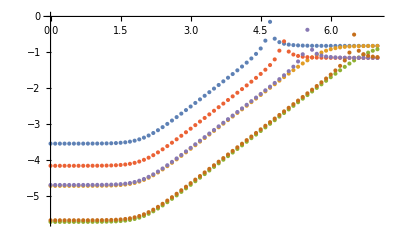

```mathematica
ListPlot[Join[boundss⟦All,All,{1,2}⟧,boundss⟦All,All,{1,3}⟧]]
```

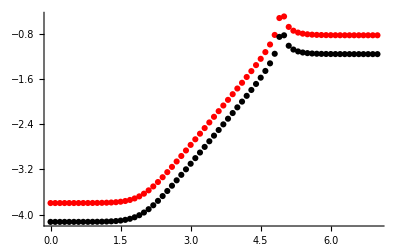

```mathematica
(*Show[{
ListPlot[boundss⟦1,All,{1,2}⟧,PlotStyle->Red],
ListPlot[boundss⟦1,All,{1,3}⟧,PlotStyle->Black]
}
,PlotRange->All]*)
```

## Generate the x parameter which will be used by "darkcast"

### for θx model

```mathematica
Clear[x]
```

```mathematica
(*guLp//simplify*)
```

simplify[guLp]

```mathematica
√((gdLp^2+gdRp^2)/2)/.θxmodel/.{QuL->-1,QdL->-1,QuR->-1,QdR->-1,QL->0,QR->0}/.gx->sθ x/.gSM′rep/.gzmz//.parameters
```

(√((-0.055175 sθ-sθ x)^2+(0.304662 sθ-sθ x)^2))/(√2)

```mathematica
$Assumptions=And[x>0,sθ>0]
simplify[xxxx_]:=(temp=xxxx/.θxmodel/.{QuL->-1,QdL->-1,QuR->-1,QdR->-1,QL->0,QR->0,QνL->0}/.gx->sθ x/.gSM′rep/.gzmz//.parameters;
temp//Simplify
)
xe=1/sθ √((gLp^2+gRp^2)/2)//simplify
(*xν=1/gx √((gνLp^2+gνRp^2)/2)//simplify*)
xν=1/sθ √(gνLp^2) //simplify(*νR most likely are be heavy, otherwise killed by BBN*)

xu=1/sθ √((guLp^2+guRp^2)/2)//simplify
xd=1/sθ √((gdLp^2+gdRp^2)/2)//simplify
```

x>0&&sθ>0

0.180493

0.359837

1. √(0.0372104+0.139137 x+1. x^2)

1. √(0.0479315-0.249487 x+1. x^2)

```mathematica
i=0;
Table[
i=i+1;
model=<||>;
model⟦"e"⟧=model⟦"mu"⟧=model⟦"tau"⟧=xe;
model⟦"nue"⟧=model⟦"numu"⟧=model⟦"nutau"⟧=xν;
model⟦"d"⟧=model⟦"s"⟧=model⟦"b"⟧=xd;
model⟦"u"⟧=model⟦"c"⟧=model⟦"t"⟧=xu;
model=model/.x->x1;
model=model//N;

str="xfs="<>ExportString[model,"PythonExpression"];
(*<>"\n"<>"rx="<>ToString[x];*)
Export[NotebookDirectory[]<>"darkcast/models/theta_x_model"<>ToString[i]<>".py",str,"Text"],
{x1,xBlist}]
```

{/home/xj/Dropbox/mywork/P2/code/darkcast/models/theta_x_model1.py,/home/xj/Dropbox/mywork/P2/code/darkcast/models/theta_x_model2.py,/home/xj/Dropbox/mywork/P2/code/darkcast/models/theta_x_model3.py}

```mathematica
model//N
```

<|tau→0.180493,mu→0.180493,e→0.180493,nutau→0.359837,numu→0.359837,nue→0.359837,b→9.8769,s→9.8769,d→9.8769,t→10.0712,c→10.0712,u→10.0712|>

### for θxBL model

```mathematica
Clear[x]
```

```mathematica
$Assumptions=And[x>0,sθ>0]
simplify[xxxx_]:=(temp=xxxx/.θxmodel/.QνL->QL/.QBminusL/.gx->sθ x/.gSM′rep/.gzmz//.parameters;
temp//Simplify
)
xe=1/sθ √((gLp^2+gRp^2)/2)//simplify
(*xν=1/gx √((gνLp^2+gνRp^2)/2)//simplify*)
xν=1/sθ √(gνLp^2) //simplify(*νR most likely are be heavy, otherwise killed by BBN*)

xu=1/sθ √((guLp^2+guRp^2)/2)//simplify
xd=1/sθ √((gdLp^2+gdRp^2)/2)//simplify
```

x>0&&sθ>0

1. √(0.0325778-0.0287869 x+1. x^2)

0.359837+x

0.333333 √(0.334893-0.41741 x+1. x^2)

0.333333 √(0.431384+0.74846 x+1. x^2)

```mathematica
i=0;
Table[
i=i+1;
model=<||>;
model⟦"e"⟧=model⟦"mu"⟧=model⟦"tau"⟧=xe;
model⟦"nue"⟧=model⟦"numu"⟧=model⟦"nutau"⟧=xν;
model⟦"d"⟧=model⟦"s"⟧=model⟦"b"⟧=xd;
model⟦"u"⟧=model⟦"c"⟧=model⟦"t"⟧=xu;
model=model/.x->x1;
model=model//N;

str="xfs="<>ExportString[model,"PythonExpression"];
(*<>"\n"<>"rx="<>ToString[x];*)
Export[NotebookDirectory[]<>"darkcast/models/theta_xBL_model"<>ToString[i]<>".py",str,"Text"],
{x1,xBLlist}]
```

{/share_D/Dropbox/mywork/P2/code/darkcast/models/theta_xBL_model1.py,/share_D/Dropbox/mywork/P2/code/darkcast/models/theta_xBL_model2.py,/share_D/Dropbox/mywork/P2/code/darkcast/models/theta_xBL_model3.py}

```mathematica
model
```

<|tau→99.9858,mu→99.9858,e→99.9858,nutau→0.359837+100.,numu→0.359837+100.,nue→0.359837+100.,b→33.4586,s→33.4586,d→33.4586,t→33.2643,c→33.2643,u→33.2643|>

### for C(chiral) model

```mathematica
Clear[x]
```

```mathematica
Table[√((gdLp^2+gdRp^2)/2)/.addV[Cmodel]/.gSM′rep/.gzmz//.parameters,
{Cmodel,Cmodel′list}]
```

{1/3 √(17/2) √(gx^2),(√(gx^2))/(√2),1/2 √(5/2) √(gx^2)}

```mathematica
$Assumptions=And[gx>0];
i=0;
Table[
i=i+1;
xνeud=1/gx{gνLp,√((gLp^2+gRp^2)/2),√((guLp^2+guRp^2)/2),√((gdLp^2+gdRp^2)/2)}/.addV[Cmodel]/.gSM′rep/.gzmz//.parameters//Simplify//N;

{xν,xe,xu,xd}=xνeud;
Print[xνeud];
model=<||>;
model⟦"e"⟧=model⟦"mu"⟧=model⟦"tau"⟧=xe;
model⟦"nue"⟧=model⟦"numu"⟧=model⟦"nutau"⟧=xν;
model⟦"d"⟧=model⟦"s"⟧=model⟦"b"⟧=xd;
model⟦"u"⟧=model⟦"c"⟧=model⟦"t"⟧=xu;

str="xfs="<>ExportString[model,"PythonExpression"];
(*<>"\n"<>"rx="<>ToString[x];*)
Export[NotebookDirectory[]<>"darkcast/models/C_model"<>ToString[i]<>".py",str,"Text"],

{Cmodel,Cmodel′list}]
```

{-1.,0.707107,0.527046,0.971825}

{0.,0.707107,0.707107,0.707107}

{-1.5,1.76777,0.353553,0.790569}

{/share_D/Dropbox/mywork/P2/code/darkcast/models/C_model1.py,/share_D/Dropbox/mywork/P2/code/darkcast/models/C_model2.py,/share_D/Dropbox/mywork/P2/code/darkcast/models/C_model3.py}